```mathematica
(*Input: a triangle T given by a list of three 2D points, a distance d that the smaller triangle should be contained in*)
(*Output: smaller triangle with distance d from each side of T given by a list of three 2D points*)
SmallerTriangle[T_,d_]:=Module[{P1=T[[1]],P2=T[[2]],P3=T[[3]],a,b,c,s,InC,InR,λ,Q1,Q2,Q3,q1,q2,q3,p1,p2,p3},
(*Length of sides of T*)
a=Norm[P3-P2];
b=Norm[P3-P1];
c=Norm[P2-P1];
(*Semiperimeter of triangle T*)
s=(a+b+c)/2;

(*Incenter of T*)
InC=(a*P1+b*P2+c*P3)/(a+b+c);
(*Inradius of T*)
InR=Sqrt[(s-a)*(s-b)*(s-c)/s];
(*Scaling factor*)
λ=1-d/InR;

(*Shifted triangle with incenter at the origin*)
Q1=P1-InC;
Q2=P2-InC;
Q3=P3-InC;

(*Scaled down triangle of above triangle*)
q1=λ*Q1;
q2=λ*Q2;
q3=λ*Q3;

(*Smaller triangle shifted back inside original T*)
p1=q1+InC;
p2=q2+InC;
p3=q3+InC;

Return[{p1,p2,p3}]
]
```

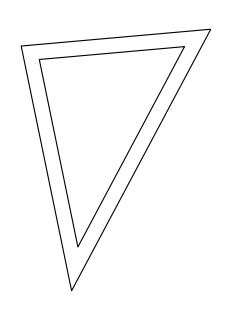

```mathematica
n=100;
(*Three random 2D points*)
T=Table[Table[RandomInteger[{-n,n}],{j,2}],{i,3}];
(*Random compatible distance*)d=RandomReal[Sqrt[((Norm[T[[3]]-T[[2]]]+Norm[T[[3]]-T[[1]]]+Norm[T[[2]]-T[[1]]])/2-Norm[T[[3]]-T[[2]]])*((Norm[T[[3]]-T[[2]]]+Norm[T[[3]]-T[[1]]]+Norm[T[[2]]-T[[1]]])/2-Norm[T[[3]]-T[[1]]])*((Norm[T[[3]]-T[[2]]]+Norm[T[[3]]-T[[1]]]+Norm[T[[2]]-T[[1]]])/2-Norm[T[[2]]-T[[1]]])/((Norm[T[[3]]-T[[2]]]+Norm[T[[3]]-T[[1]]]+Norm[T[[2]]-T[[1]]])/2)]];

Graphics[{EdgeForm[{Black,Opacity[1]}],FaceForm[{Black,Opacity[0]}],Triangle[T],Triangle[SmallerTriangle[T,d]]}]
```

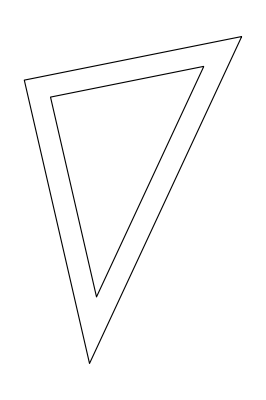

```mathematica
(*Outer triangle*)
T={{5,5},{-2,-10},{-5,3}};
(*Distance from outer triangle*)
d=1;
(*Inner triangle of distance d from T*)
t=SmallerTriangle[T,d];
(*Plot of the triangles*)
Graphics[{EdgeForm[{Black,Opacity[1]}],FaceForm[{Black,Opacity[0]}],Triangle[T],Triangle[t]}]
```